# Quantum Magnets + Impurity

This script employs exact diagonalization to compute the magnon spectrum and spin expectation values in  Quantum Magnets featuring a magnetic impurity.  We use the a spin Hamiltonian  in the Honeycomb lattice plus the magnetic Zeeman term for the bulk spin, and an antiferromagnetic (Heisenberg like) Kondo coupling of the impurity spin to the bulk. The impurity is couple to one site in the Adatom case and to three sites in the Substitutional case. We will consider
	•   spin 1/2 system with a impurity spin Simp= 1/2,1, or 3/2 [ e.g.  RuCl_3 with Simp=3/2 Cr^(3+)  impurity (e.g. 1704.03849 ) ]

In this Notebook we are preparing figures for the XXZ model :                                                                       
	•  Run  “XXZ.m”  to get the data for the according system size
	•  The function are defined in the package  “definition.wl”

```mathematica
Quit[]
```

## Preamble

```mathematica
Needs["MaTeX`"]

If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];

Get[ FileNameJoin[{Directory[],"definitions.wl" }] ];

figFolder =FileNameJoin[{NotebookDirectory[],"Figures" }];
createDirectory@figFolder;

opensMarker[coln_]:=Graphics[{coln[[1]],EdgeForm@Directive[coln[[1]],Thickness[.08]],Opacity[0.3],RegularPolygon[coln[[2]]]  }];
```

Figures-XXZ-h

```mathematica
cyan=CMYKColor[.70,.20,0,0.2];
magenta=CMYKColor[0,.40,.31,0.1];
pink=CMYKColor[0,.91,.46,.08];
red=CMYKColor[0,.89,.88,.12];
blue=CMYKColor[1,.36,0,.40];
green=CMYKColor[.56,0,.58,.31];
```

## Figures - Adatom Case

Information/Parameters

eigenvalues and energy level are saved as
		. )  eValues and
		..)  eLevels
	with Context =  Ada/Sub, size LxLy, and  S spin imp
	e.g.  context=Ada33S15 for (Lx,Ly)=(3,3) and simp=3/2

```mathematica
plotRange={-.02,.52};
```

### Kitaev ADA

#### (2,2) code spin 1/2

```mathematica
Begin["KitaevAda22S05`"]; 

$FileName="Kitaev-g5.m";systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
impuritySpin     = {3/2};
gs               = {5};
KondoCoupling    = {.5};
hRange           = {0,3,1.5/10};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 10; 
HamCoupling="Kitaev_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{bulk}}=S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"si"->ToString[N@impuritySpin],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-g5\Kitaev_FM_ADA_size=(2,2)_Simp=1.5\h=Range[0,3,0.15]_JK={0.5}_k=10.txt

$Aborted

KitaevAda22S05`

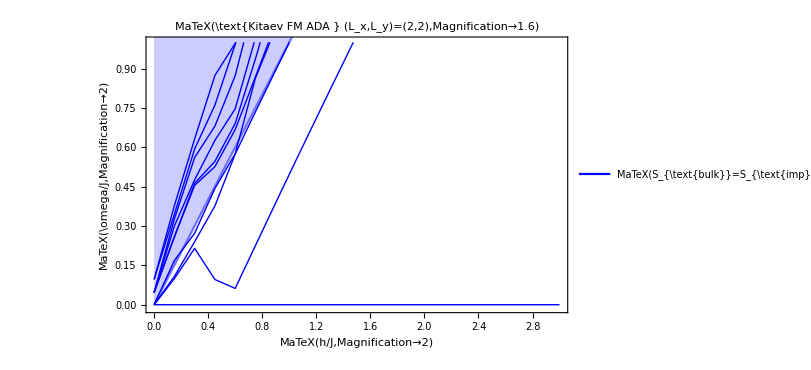

FigSpin

FigSpinOther

```mathematica
Begin["KitaevAda22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### (3,3) code spin 3/2 g=5

```mathematica
Begin["KitaevAda33S15`"]; 
$FileName="Kitaev-g5.m";

systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
impuritySpin     = {3/2};
gs               = {5};
KondoCoupling    = {.5};
hRange           = {0,1.2,1.2/40};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 10; 
HamCoupling="Kitaev_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["g=g0, \\, S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"si"->ToString[N@impuritySpin],"g0"->ToString[N@g],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.13]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
(*, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]*)
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]] ];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]  ];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]   ];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-g5\Kitaev_FM_ADA_size=(3,3)_Simp=1.5\h=Range[0,1.2,0.03]_JK={0.5}_k=10.txt

$Aborted

KitaevAda33S15`

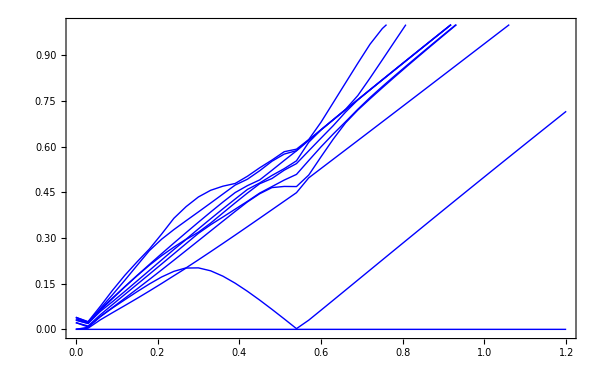

FigSpin

FigSpinOther

```mathematica
Begin["KitaevAda33S15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

### XXZ FM ADA (2,2)

#### code spin 1/2

```mathematica
Begin["Ada22S05`"]; 

$FileName="XXZ-h.m";
systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,1.5,.03};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 20; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{bulk}}=S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"si"->ToString[N@impuritySpin],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,1.5,0.03]_JK={0.5}_k=20.txt

$Aborted

Ada22S05`

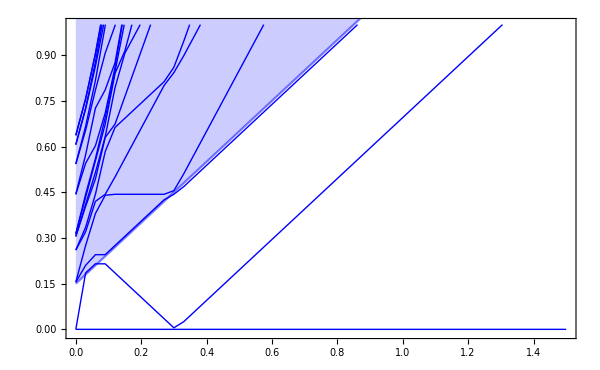

FigSpin

FigSpinOther

```mathematica
Begin["Ada22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code spin 1 bulk 1

```mathematica
Begin["Ada22S11`"]; 

$FileName="XXZ-h-1.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {1};
impuritySpin     = {1};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.2};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 10; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;      Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[N@impuritySpin],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

h Range length= 11

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-1.5\XXZ_FM_ADA_size=(2,2)_Simp=1.0\h=Range[0,2,0.2]_JK={0.5}_k=10.txt

$Aborted

Ada22S11`

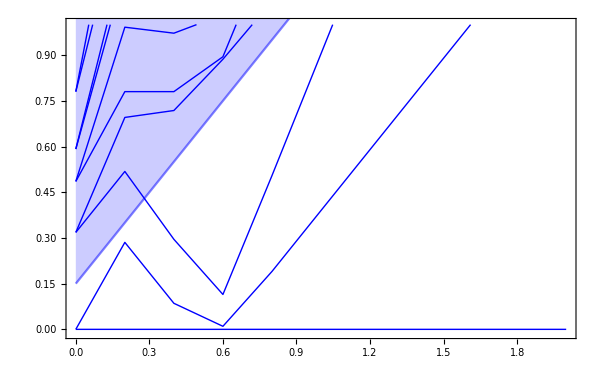

FigSpin

FigSpinOther

```mathematica
Begin["Ada22S11`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code s=simp=3/2

```mathematica
Begin["Ada22Sbulk15`"]; 
$FileName="XXZ-h-1.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {3/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.1};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 10; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;       
Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;5]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,2}  ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;
	
figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

h Range length= 21

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-1.5\XXZ_FM_ADA_size=(2,2)_Simp=1.5\h=Range[0,2,0.1]_JK={0.5}_k=10.txt

$Aborted

Ada22Sbulk15`

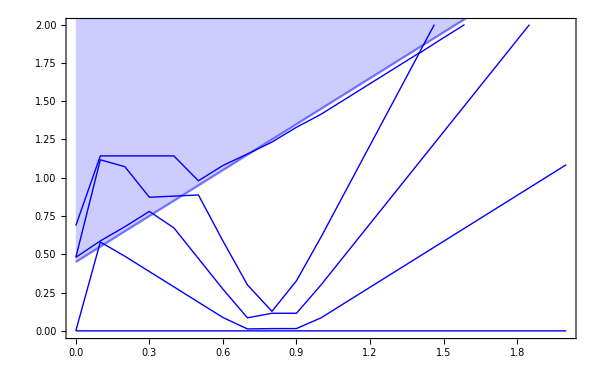

FigSpin

FigSpinOther

```mathematica
Begin["Ada22Sbulk15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code s=3/2 simp=1/2 (!!)

```mathematica
Begin["Ada22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 50; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;
 
Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ](*
, Plot[  2Sbulk( 3/2 Norm[λn])+h+.001,{h,Min@hRange,Max@hRange},PlotStyle->{White}, Filling->Top,FillingStyle->Opacity[1]]*)
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Thick}, Filling->Top]
] ;
	
figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
]
End[]
```

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_k=50.txt

$Aborted

Ada22Sbulk15simp05`

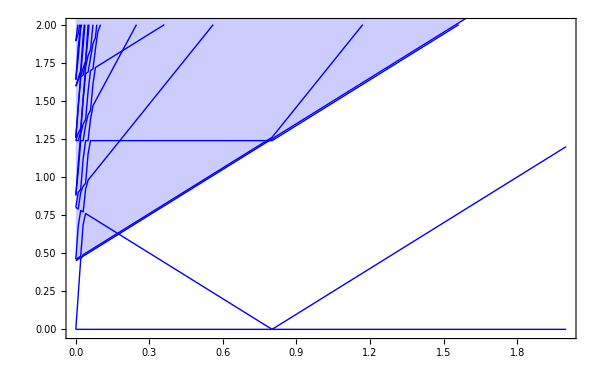

FigSpin

FigSpinOther

```mathematica
Begin["Ada22Sbulk15simp05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### export

```mathematica
Begin["Ada22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Begin["Ada22S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S05"<>".pdf" }],   Ada22S05`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S05"<>".pdf"  }],  Ada22S05`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S1"<>".pdf"  }],  Ada22S1`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S1"<>".pdf"  }],  Ada22S1`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S15"<>".pdf" }],   Ada22S15`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S15"<>".pdf"  }],  Ada22S15`FigSpin ];
```

### XXZ FM ADA (3,3)

#### code spin 1/2 (!!)

```mathematica
Begin["Ada33S05`"]; 

$FileName="XXZ-h.m";

systemDimensions = {{3,3}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,1.5,1.5/20};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 10; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;3]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["g=g0,\\, S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"g0"->ToString[g],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.15]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {{0,1},{-.01,.8} } ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h\XXZ_FM_ADA_size=(3,3)_Simp=0.5\h=Range[0,1.5,0.075]_JK={0.5}_k=10.txt

$Aborted

Ada33S05`

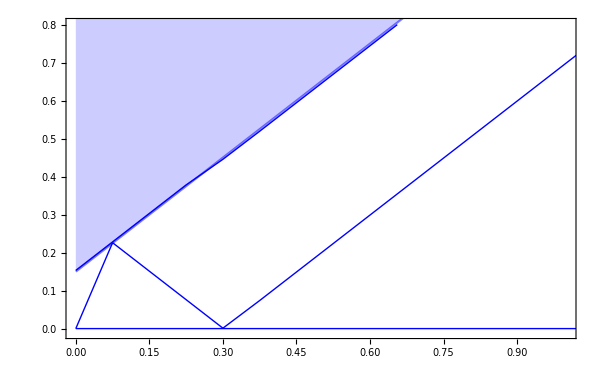

FigSpin

FigSpinOther

```mathematica
Begin["Ada33S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

### Disp XXZ ADA LSW S=3/2 Simp=1/2 (!!)

```mathematica
JkValues[[1;;16]]
```

{0.05,0.0966667,0.143333,0.19,0.236667,0.283333,0.33,0.376667,0.423333,0.47,0.516667,0.563333,0.61,0.656667,0.703333,0.75}

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_k=50.txt

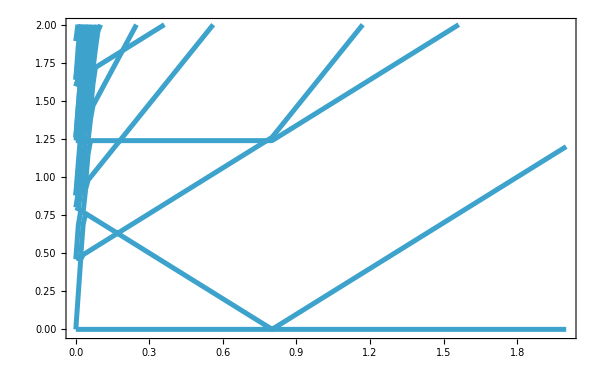
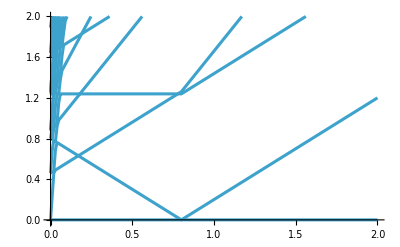
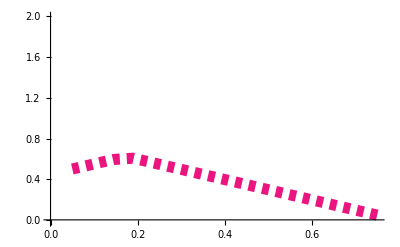
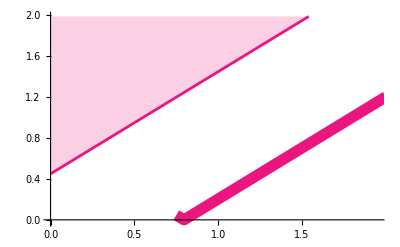

-Graphics-

Ada22Sbulk15simp05`

```mathematica
Begin["Ada22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 50; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;
 
Print["h Range length= ",Length@hRange];

dataLSW=Module[{file,path,data},
path= FileNameJoin@{ NotebookDirectory[],"data","data_XXZ_ada.txt" };
file=OpenRead[path];
data=Interpreter["Number"]/@(StringSplit[ #,";"]&/@ReadList[file,Record,RecordSeparators->{"\n"} ]);
(*data= ReadList[file,Number,RecordLists->True];*)
Close[file];
data
];
JkValues = dataLSW[[1]];
EnValues=1.5 Transpose[  dataLSW[[2;;-1]]  ];
JkDisp =Thread@ {JkValues, EnValues  };



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;(*
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	*)

	plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]  ;

(*figDispLSWcont=Show[ListPlot[ Transpose[Thread/@JkDisp][[2;;-1]],PlotStyle->{{Magenta,Thickness[0.006],Opacity[0.95] }},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange->{ {0.75,2},{-.02,2}}   ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Magenta,Thick}, Filling->Top,
PlotRange->{ {0,2},{-.02,2}}] ];*)
figDispLSWbs=Show[
ListPlot[  Transpose[Thread/@JkDisp[[16;;-1]] ][[1]] ,PlotStyle->{{color2,Thickness[0.02],Opacity[1] }},Joined->True,PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
PlotRange->{ {0,1.95},{-.02,1.99}}   ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{color2,Thickness[0.005]}, Filling->Top,
PlotRange->{ {0,2},{-.02,1.99}}] 
];

figDispLSWbsDash=ListPlot[Transpose[Thread/@JkDisp[[1;;16]]][[1]],PlotStyle->{{color2,Dashed,Thickness[0.02],Opacity[1] }},Joined->True,
PlotRange->{ {0,0.75},{-.02,2}}   ];

figDispED=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.0055] ,Opacity[1]}},Joined->True,
PlotRange-> {-.02,2}  ] ;
]


Print[figDispED0,figDispED, figDispLSWbsDash,figDispLSWbs]

figDisp=Show[figDispED0, figDispLSWbsDash,figDispLSWbs,figDispED,
PlotRange->{ {0,2},{-.02,2.03}}]
End[]
```

```mathematica
(*Module[{plotLegend,g=1,JK=0.5,sb=1.5,si=.5},

	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@si ],"sb"->ToString[TeXForm@Rationalize@N@sb ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[0.1]
}] ;

ListPlot[Transpose[Thread/@JkDisp],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]
]*)
```

```mathematica
(*Number[StringReplace[dataLSW[[1,1]], "e"->"*^"]]*)
```

### Spin XXZ ADA LSW S=3/2 Simp=1/2 (!!)

```mathematica
Begin["Ada22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 50; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;
 
Print["h Range length= ",Length@hRange];

dataLSW=Module[{file,path,data},
path= FileNameJoin@{ NotebookDirectory[],"data","data_XXZ_ada.txt" };
file=OpenRead[path];
data=Interpreter["Number"]/@(StringSplit[ #,";"]&/@ReadList[file,Record,RecordSeparators->{"\n"} ]);
(*data= ReadList[file,Number,RecordLists->True];*)
Close[file];
data
];
JkValues = dataLSW[[1]];
EnValues=1.5 Transpose[  dataLSW[[2;;-1]]  ];
JkDisp =Thread@ {JkValues, EnValues  };


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},

	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};

	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };


FigSpinED=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];

	plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]  ;
figDispLSWbs=Show[
ListPlot[  Transpose[Thread/@JkDisp[[16;;-1]] ][[1]] ,PlotStyle->{{color2,Thickness[0.02],Opacity[1] }},Joined->True,PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
PlotRange->{ {0,1.95},{-.02,1.99}}   ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{color2,Thickness[0.005]}, Filling->Top,
PlotRange->{ {0,2},{-.02,1.99}}] 
];

figDispLSWbsDash=ListPlot[Transpose[Thread/@JkDisp[[1;;16]]][[1]],PlotStyle->{{color2,Dashed,Thickness[0.02],Opacity[1] }},Joined->True,
PlotRange->{ {0,0.75},{-.02,2}}   ];

figDispED=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.0055] ,Opacity[1]}},Joined->True,
PlotRange-> {-.02,2}  ] ;
]


Print[figDispED0,figDispED, figDispLSWbsDash,figDispLSWbs]

figDisp=Show[figDispED0, figDispLSWbsDash,figDispLSWbs,figDispED,
PlotRange->{ {0,2},{-.02,2.03}}]
End[]
```

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_k=50.txt

-Graphics--Graphics--Graphics--Graphics-

-Graphics-

Ada22Sbulk15simp05`

```mathematica
(*Module[{plotLegend,g=1,JK=0.5,sb=1.5,si=.5},

	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@si ],"sb"->ToString[TeXForm@Rationalize@N@sb ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[0.1]
}] ;

ListPlot[Transpose[Thread/@JkDisp],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]
]*)
```

```mathematica
(*Number[StringReplace[dataLSW[[1,1]], "e"->"*^"]]*)
```

## Figures - Substitution Case

```mathematica
plotRange={-.02,.4};
```

### Kitaev SUB

#### (2,2) code spin 3/2

```mathematica
Begin["KitaevSub22S15`"]; 
$FileName="Kitaev-g5.m";

systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
impuritySpin     = {3/2};
gs                             = {7};
KondoCoupling    = {.5010};
hRange           = {0,1,1./20};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 10; 
HamCoupling="Kitaev_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["g=g0, \\, S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"g0"->ToString[N@g],"si"->ToString[N@impuritySpin],"jk"->ToString[ round[JK,100]  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-g5\Kitaev_FM_SUB_size=(2,2)_Simp=1.5\h=Range[0,1,0.05]_JK={0.501}_k=10.txt

$Aborted

KitaevSub22S15`

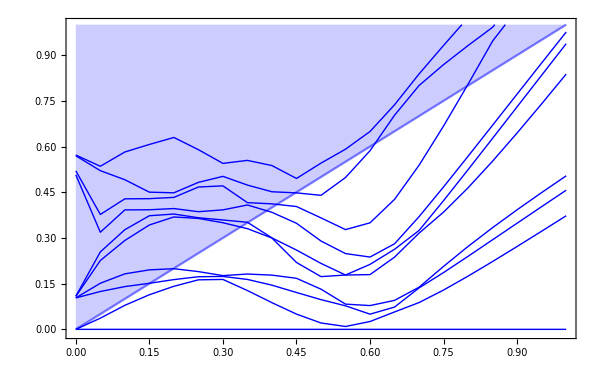

FigSpin

FigSpinOther

```mathematica
Begin["KitaevSub22S15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### (3,3) code spin 3/2

```mathematica
Begin["KitaevSub33S15`"]; 
$FileName="Kitaev-g5.m";

systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
impuritySpin     = {3/2};
gs               = {5};
KondoCoupling    = {.5};
hRange           = {0,1.2,1.2/40};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 10; 
HamCoupling="Kitaev_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["g=g0, \\, S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"si"->ToString[N@impuritySpin],"g0"->ToString[N@g],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.13]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
(*, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]*)
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]] ];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]  ];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]   ];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-g5\Kitaev_FM_SUB_size=(3,3)_Simp=1.5\h=Range[0,1.2,0.03]_JK={0.5}_k=10.txt

$Aborted

KitaevSub33S15`

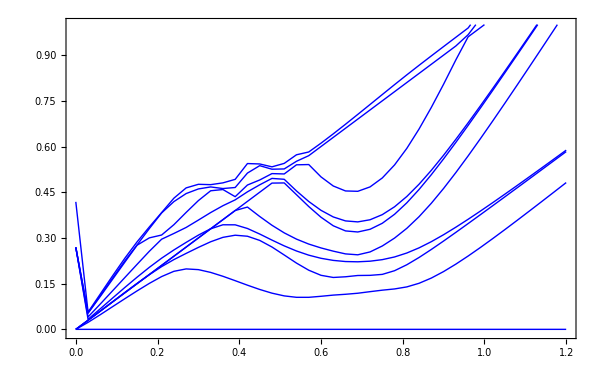

FigSpin

FigSpinOther

```mathematica
Begin["KitaevSub33S15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

### XXZ FM SUB (2,2)

#### code spin 1/2

```mathematica
Begin["Sub22S05`"]; 

$FileName="XXZ-h.m";systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
impuritySpin     = {1/2};
gs               = {0.57};
KondoCoupling    = {.5};
hRange           = {0,1.1,.03};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 120; 
HamCoupling="XXZ_FM_SUB";

dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;      Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk , \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

h Range length= 37

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,1.1,0.03]_JK={0.5}_k=120.txt

$Aborted

Sub22S05`

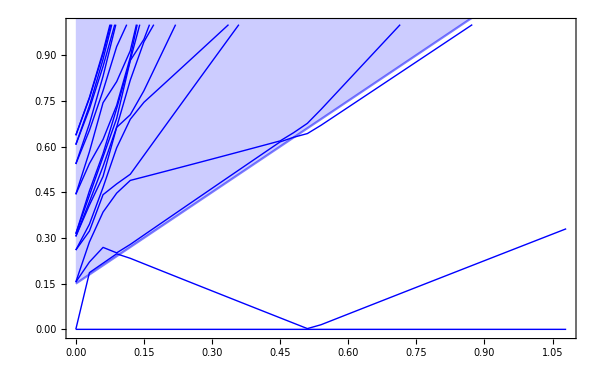

FigSpin

FigSpinOther

```mathematica
Begin["Sub22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code s=simp=3/2

```mathematica
Begin["Sub22Sbulk15`"]; 
$FileName="XXZ-h-1.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {3/2};
gs               = {0.57};
KondoCoupling    = {.5};
hRange           = {0,8,.2};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 6; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;   
Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;4]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,3}  ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h+.001,{h,Min@hRange,Max@hRange},PlotStyle->{White}, Filling->Top,FillingStyle->Opacity[1]]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Thick}, Filling->Top]
] ;
	
figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
]
End[]
```

h Range length= 41

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-1.5\XXZ_FM_SUB_size=(2,2)_Simp=1.5\h=Range[0,8,0.2]_JK={0.5}_k=6.txt

$Aborted

Sub22Sbulk15`

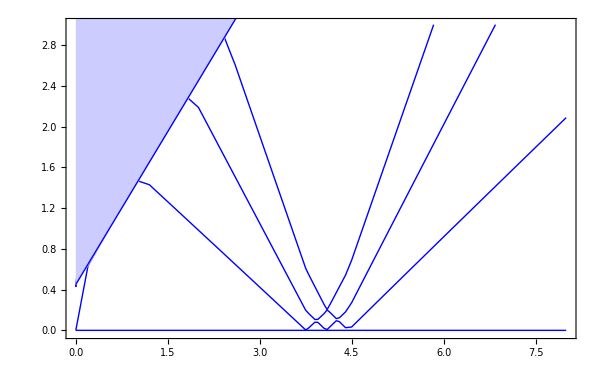

FigSpin

FigSpinOther

```mathematica
Begin["Sub22Sbulk15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

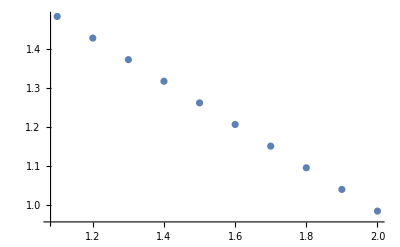

{a→-0.557073,b→3.76535}

```mathematica
Begin["Sub22Sbulk15`"]; 

ListPlot[ Transpose[Thread/@levels][[2]][[-10;;-1]] ]
 FindFit[   Transpose[Thread/@levels][[2]][[-10;;-1]]    ,  a (x-b), {{a,-.5},{b,4}},x]

End[];
```

```mathematica
a (x-b)/.{a->-0.5570734482159516,b->3.765349535481436}
```

-0.557073 (-3.76535+x)

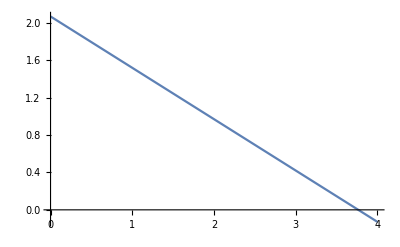

```mathematica
Plot[    -0.55 (-3.765349 +x)   ,{x,0,4}]
```

#### code s=3/2 simp=1/2 (!!)

```mathematica
Begin["Sub22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5-2.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,5,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 40; 

HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;   
Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;klevels]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,3}  ]
(*, Plot[  2Sbulk( 3/2 Norm[λn])+h+.001,{h,Min@hRange,Max@hRange},PlotStyle->{White}, Filling->Top,FillingStyle->Opacity[1]]*)
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Thick}, Filling->Top]
] ;
	
figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];

FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
]
End[]
```

h Range length= 251

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5-2\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,5,0.02]_JK={0.5}_k=40.txt

$Aborted

Sub22Sbulk15simp05`

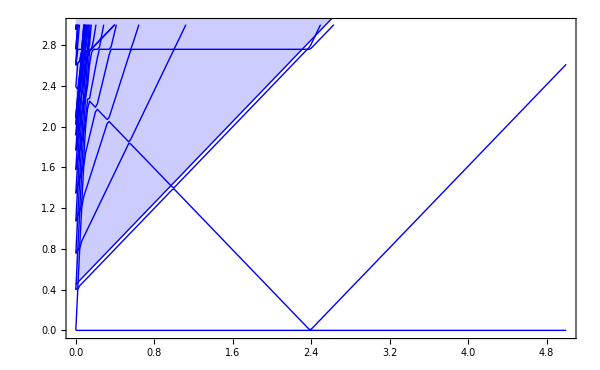

FigSpin

FigSpinOther

```mathematica
Begin["Sub22Sbulk15simp05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]     ]  *)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Begin["Sub22Sbulk15`"]; 

ListPlot[ Transpose[Thread/@levels][[2]][[-10;;-1]] ]
 FindFit[   Transpose[Thread/@levels][[2]][[-10;;-1]]    ,  a (x-b), {{a,-.5},{b,4}},x]

End[];
```

-Graphics-

{a→-0.557073,b→3.76535}

```mathematica
a (x-b)/.{a->-0.5570734482159516,b->3.765349535481436}
```

-0.557073 (-3.76535+x)

```mathematica
Plot[    -0.55 (-3.765349 +x)   ,{x,0,4}]
```

-Graphics-

#### export

```mathematica
Begin["Ada22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Begin["Ada22S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S05"<>".pdf" }],   Ada22S05`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S05"<>".pdf"  }],  Ada22S05`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S1"<>".pdf"  }],  Ada22S1`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S1"<>".pdf"  }],  Ada22S1`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S15"<>".pdf" }],   Ada22S15`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S15"<>".pdf"  }],  Ada22S15`FigSpin ];
```

### XXZ FM SUB (3,3)

#### code spin 1/2 (!!)

```mathematica
(*MaTeX["\\begin{array}{l} S_{\\text{bulk}}=S_{\\text{imp}}=si, \\\\[5pt] g=g0,\\,J_{\\mathrm{K}}=jk
\\end{array}",Magnification->2]*)
```

```mathematica
Begin["Sub33S05`"]; 
$FileName="XXZ-h.m";

systemDimensions = {{3,3}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,2./50};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 3; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;        Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,nl}, nl=klevels;
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
ev=eValues;
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;nl]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["\\begin{array}{l} S_{\\text{bulk}}=S_{\\text{imp}}=si, \\\\[5pt] g=g0,\\,J_{\\mathrm{K}}=jk
\\end{array}",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"g0"->ToString[Round@g],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.15]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Hue[0.5,0,0.7,0.8],Background->Hue[0,0,1,0.8]]&)(*"Panel"*)],{Scaled[{.001,1}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {All,{-.01,1} } ]
, Plot[ (* 2Simp*) 3/2 Norm[λn]+  h,{h,Min@hRange,Max@hRange},PlotRange->{0,1},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.02,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  Sort@dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
figEn
]
End[]
```

h Range length= 51

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h\XXZ_FM_SUB_size=(3,3)_Simp=0.5\h=Range[0,2,0.04]_JK={0.5}_k=3.txt

$Aborted

Sub33S05`

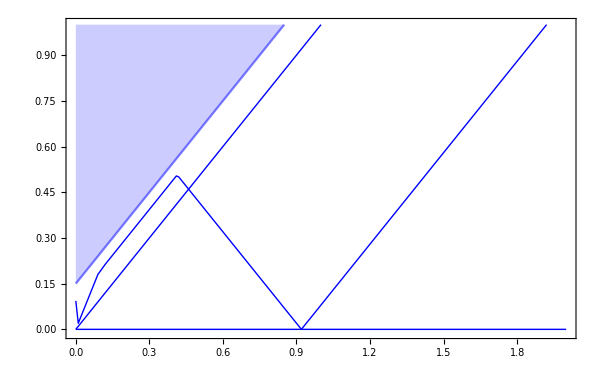

FigSpin

FigSpinOther

```mathematica
Begin["Sub33S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

### XXZ SUB LSW S=3/2 Simp=1/2 (!!)

```mathematica
JkValues[[1;;6]]
```

{0.05,0.2,0.35,0.5,0.65,0.8}

h Range length= 251

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5-2\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,5,0.02]_JK={0.5}_k=40.txt

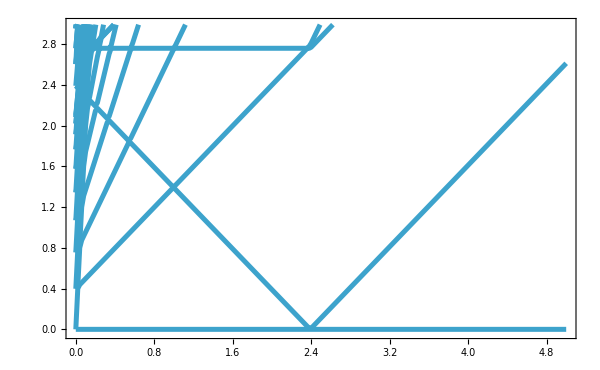
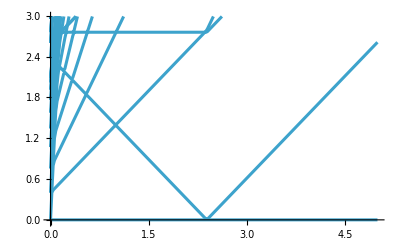
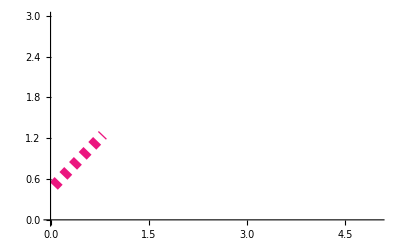
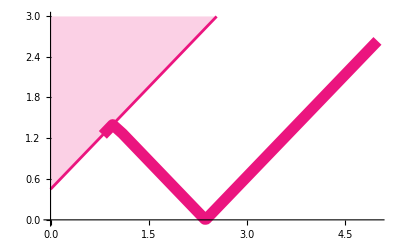

-Graphics-

Sub22Sbulk15simp05`

```mathematica
Begin["Sub22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5-2.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,5,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 40; 

HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  
 
Print["h Range length= ",Length@hRange];

dataLSW=Module[{file,path,data},
path= FileNameJoin@{ NotebookDirectory[],"data","data_XXZ_sub.txt" };
file=OpenRead[path];
data=Interpreter["Number"]/@(StringSplit[ #,";"]&/@ReadList[file,Record,RecordSeparators->{"\n"} ]);
(*data= ReadList[file,Number,RecordLists->True];*)
Close[file];
data
];
JkValues = dataLSW[[1]];
EnValues=1.5 Transpose[  dataLSW[[2;;-1]]  ];
JkDisp =Thread@ {JkValues, EnValues  };



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,prange={ {0,5},{-.03,2.99}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;(*
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	*)

	plotTitle  = StringReplace[StringJoin[{"\\text{Substitution} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> prange    ]  ;

(*figDispLSWcont=Show[ListPlot[ Transpose[Thread/@JkDisp][[2;;-1]],PlotStyle->{{Magenta,Thickness[0.006],Opacity[0.95] }},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange->{ {0.75,2},{-.02,2}}   ]
, Plot[  2Sbulk( (3/2) Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Magenta,Thick}, Filling->Top,
PlotRange->{ {0,2},{-.02,2}}] ];*)
figDispLSWbs=Show[
ListPlot[  Transpose[Thread/@JkDisp[[6;;-1]] ][[1]] ,PlotStyle->{{color2,Thickness[0.02],Opacity[1] }},Joined->True,PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
PlotRange->prange]
, Plot[  2Sbulk( (3/2) Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{color2,Thickness[0.005]}, Filling->Top,
PlotRange->prange   ] 
];

figDispLSWbsDash=ListPlot[Transpose[Thread/@JkDisp[[1;;6]]][[1]],PlotStyle->{{color2,Dashed,Thickness[0.02],Opacity[1] }},Joined->True,
PlotRange->prange   ];

figDispED=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.0055] ,Opacity[1]}},Joined->True,
PlotRange-> prange   ] ;
]


Print[figDispED0,figDispED, figDispLSWbsDash,figDispLSWbs]

figDisp=Show[figDispED0, figDispLSWbsDash,figDispLSWbs,figDispED,
PlotRange->{ {0,4.8},{-.03,3.02}}    ]
End[]
```

```mathematica
(*Module[{plotLegend,g=1,JK=0.5,sb=1.5,si=.5},

	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@si ],"sb"->ToString[TeXForm@Rationalize@N@sb ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[0.1]
}] ;

ListPlot[Transpose[Thread/@JkDisp],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]
]*)
```

```mathematica
(*Number[StringReplace[dataLSW[[1,1]], "e"->"*^"]]*)
```